## The error function

## Katharine Long Texas Tech University

### Definition of the error function

The error function erf(x) is defined by the definite integral

erf(x)=2/(√π)∫_0^x e^(-t^2)ⅆt.

This integral cannot be evaluated in closed form except for x=0 and x→±∞. The values at those points are erf(0)=0 and erf(±∞)=±1.

#### Computing the error function in Mathematica

The function Erf[x] returns the error function. You can assume that it will be computed to high accuracy.

#### Visualizing the error function

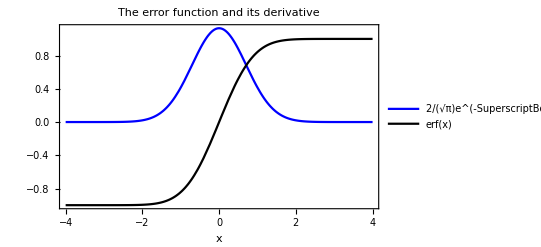

```mathematica
Plot[{2/Sqrt[Pi]Exp[-x^2], Erf[x]},{x,-4,4},PlotStyle->{Blue,Black},FrameLabel->{"x"},PlotLegends->Placed[{"2/(√π)e^(-SuperscriptBox[x, 2])","erf(x)"},{Right,Bottom}],PlotLabel->"The error function and its derivative"]
```

### Maclaurin series

The Maclaurin series for erf(x) is easily derived by integrating the Maclaurin series for the Gaussian. It is convergent for all x∈ℂ.

```mathematica
S[n_,x_]:=Normal[Series[Erf[x],{x,0,n}]]
```

```mathematica
s2[x_]=S[2,x];
```

```mathematica
s4[x_]=S[4,x];
```

```mathematica
s8[x_]=S[8,x];
```

```mathematica
s16[x_]=S[16,x]
```

-x^15/(37800 √π)+x^13/(4680 √π)-x^11/(660 √π)+x^9/(108 √π)-x^7/(21 √π)+x^5/(5 √π)-(2 x^3)/(3 √π)+(2 x)/(√π)

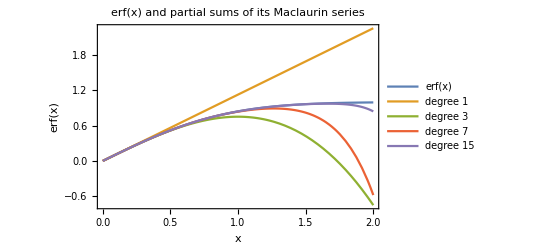

```mathematica
Plot[{Erf[x],s2[x],s4[x],s8[x],s16[x]},{x,0,2},
PlotLegends->Placed[{"erf(x)", "degree 1", "degree 3", "degree 7", "degree 15"},{Left,Top}],
FrameLabel->{"x","erf(x)"},
PlotLabel->"erf(x) and partial sums of its Maclaurin series"]
```

### Asymptotic expansion

The asymptotic expansion for erf(x) does not converge as n→ ∞ for any x. However, for fixed n, it converges as x→ ∞. It is an effective approximation to erf(x) when x is large.

```mathematica
A[M_,x_]:=1-Exp[-x^2]/Sqrt[Pi]/x (1 - Sum[(-1)^n(2n-1)!!/2^n/x^(2n),{n,1,M}])
```

```mathematica
a0[x_]=A[0,x]
```

1-(ⅇ^(-x^2))/(√π x)

```mathematica
a4[x_]=A[4,x];
```

```mathematica
a10[x_]=A[10,x]
```

1-(ⅇ^(-x^2) (1/(2 x^2)-3/(4 x^4)+15/(8 x^6)-105/(16 x^8)+945/(32 x^10)-10395/(64 x^12)+135135/(128 x^14)-2027025/(256 x^16)+34459425/(512 x^18)-654729075/(1024 x^20)+1))/(√π x)

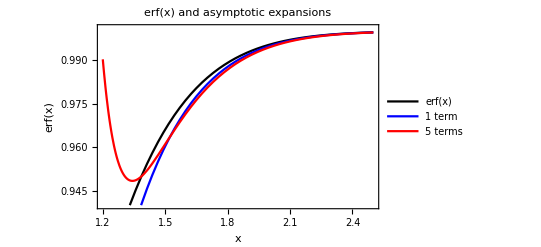

```mathematica
Plot[{Erf[x],a0[x],a4[x]},{x,1.2,2.5},PlotRange->{0.94,1.001},FrameLabel->{"x","erf(x)"},PlotStyle->{Black,Blue,Red},
PlotLegends->Placed[{"erf(x)", "1 term", "5 terms"},{Center,Right}],PlotLabel->"erf(x) and asymptotic expansions"]
```